```mathematica
thing
```

Pseudo Code:
Graph G = network graph
Define number of labels
Number verticies starting with rogue node 0 and working from the location of this node outwards
FOR all labels
IF label_vertex 6 and 7 connected?

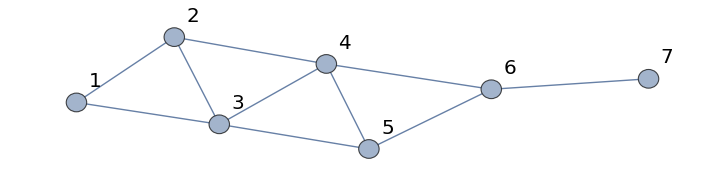

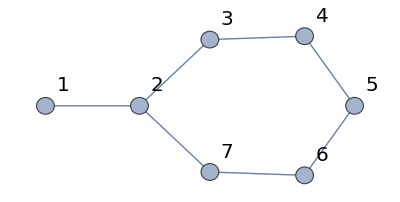

```mathematica
edges = {1<-> 2,2<->3,3<->4,1<->4,1<->3,2<->4,4<->6,4<->5,3<->5,3<->6,5<->6,10<->11,11<->9,10<->9,10<->8,8<->9,7<->9,7<->8,8<->12,7<->13,7<->12,12<->13,13<->15,14<->15,14<->13,12<->14,12<->15};
edgesS = {4<->5,5<->3,4<->3,4<->2,2<->3,1<->3,1<->2,5<->6,4<->6,6<->7};
verticies = {1,2,3,4,5,6,7,8,9,10,11,12,13,14,15};
EH = Graph[edges];
EHnotNorth = Graph[edgesS];
Show[SetProperty[%,{VertexLabels->"Name", VertexSize -> .2, EdgeStyle -> Thick,VertexLabelStyle->Directive[Black,Italic,20]}]]
oG = Graph[{1<->2,2<->3,3<->4,4<->5,5<->6,6<->7,7<->2}];
Show[SetProperty[%,{VertexLabels->"Name", VertexSize -> .2, EdgeStyle -> Thick,VertexLabelStyle->Directive[Black,Italic,20]}]]
```

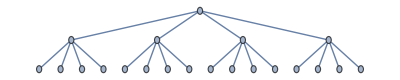

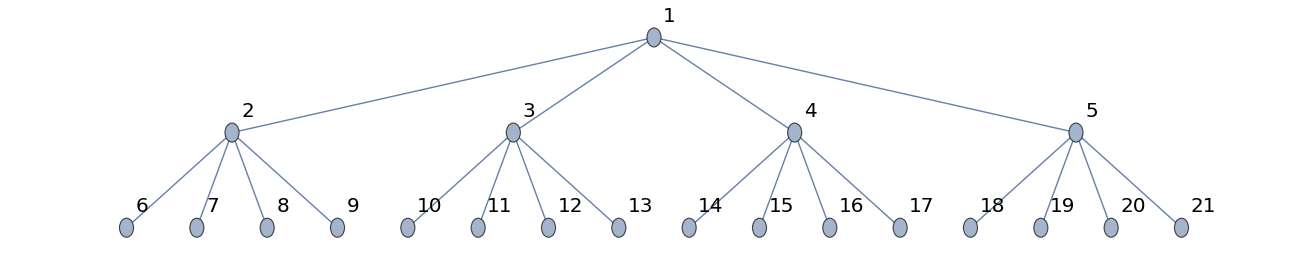

```mathematica
numChannels = 4;
numNodes = 3;
og = CompleteKaryTree[numNodes,numChannels]
Show[SetProperty[%,{VertexLabels->"Name", VertexSize -> .2, EdgeStyle -> Thick,VertexLabelStyle->Directive[Black,Italic,20]}]]
```

```mathematica
g = og;
G = EHnotNorth;
modOffset = 0;
For[i = 2, i≤ numNodes, i++,
	adj2 = AdjacencyList[G,i,2]; (*Make list of vertices "adjacent" (1 or 2 away) on G to ap i*)
	adj1 = AdjacencyList[G,i]; (*Make list of vertices adjacent (1 away) on G to ap i*)
	problems1 = Select[adj1,#< i &]; (*Selects part of adjacency list that will have already been defined at this point in the algorithm (ap # < i)*)
	problems2 = Select[adj2,#< i &]; (*Selects part of adjacency list that will have already been defined at this point in the algorithm (ap # < i)*)
	nodes = Range[1+Sum[numChannels^(k-1),{k,1,i-1}],Sum[numChannels^(k-1),{k,1,i}]]; (*row of channel assignment options for this ap given previous assignment *)
	For[ j=1, j≤Length[nodes],j++,(* Iterates through options in this row and will remove all verticies that are not valid solutions based on previous assignments *)
	vertex = nodes[[j]]; (* Define "vertex" to be the vertex that we are currently investigating *)
	path = FindShortestPath[g,1,vertex];(* Finds one and only path to root *)
	If [path =={},
		g = VertexDelete[g,vertex];
		Continue[];
	];
	channelAssignment = Mod[Most[path],numChannels,modOffset];(* Showing channel assignment of all of the verticies in the path *)
	adjacent2AssignedChannels= Part[channelAssignment,problems2]; (* All things "adjacent" to the AP that have already been assigned at this point in the algorithm *)
	adjacent1AssignedChannels= Part[channelAssignment,problems1]; (* All things "adjacent" to the AP that have already been assigned at this point in the algorithm *)
	If[ MemberQ[adjacent2AssignedChannels,Mod[vertex,numChannels,modOffset]], (* Checks if channel assignment interferes with previous assignment of "adjacent"(1 or 2) APs*)
		g = VertexDelete[g,vertex]; (* Deletes vertex on tree if channel assignment for AP in question is NOT legal*)
		Continue[];
	];
	For[k = 1, k≤ Length[adjacent1AssignedChannels],k++, (* Checks if adjacent APs are less than or equal to 1 away and deletes vertex if they are *)
	If[Abs[adjacent1AssignedChannels[[k]]-Mod[vertex,numChannels,modOffset]]≤ 1,
		g = VertexDelete[g,vertex];
		Break[];
	]	
	];
	];
	];
```

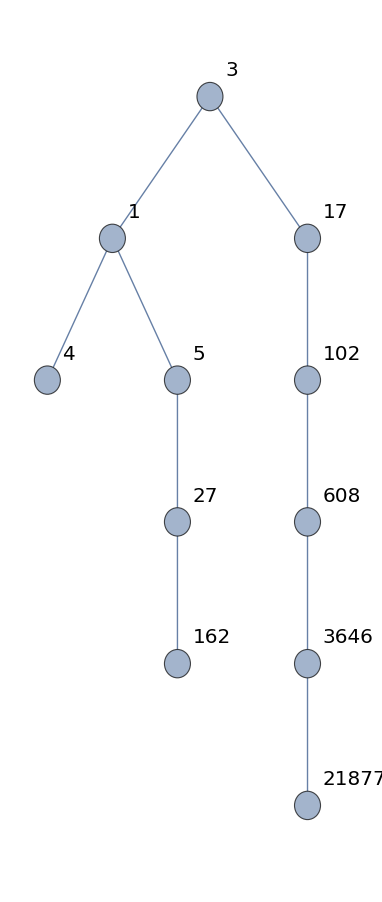

{{1,3,5,0,2,4,1}}

```mathematica
survivorVertices = Flatten[WeaklyConnectedComponents[g,{1}]];
finTree = Subgraph[g,survivorVertices];
Show[SetProperty[%,{VertexLabels->"Name", VertexSize -> .2, EdgeStyle -> Thick,VertexLabelStyle->Directive[Black,Italic,20]}]]
endpoints = Range[1+Sum[numChannels^(k-1),{k,1,numNodes-1}],Sum[numChannels^(k-1),{k,1,numNodes}]];
assignments = {};
For[ n= 1, n ≤ Length[endpoints], n++,
If[ ContainsAny[Flatten[VertexList[finTree]],{endpoints[[n]]}],
AppendTo[assignments,FindShortestPath[finTree,1,endpoints[[n]] ]]
];
];
Mod[assignments,numChannels,modOffset]
```

```mathematica
Mod[{1,3,15,72,359,1796},5,2]
```

{6,3,5,2,4,6}